```mathematica
SatisfiabilityInstances
```

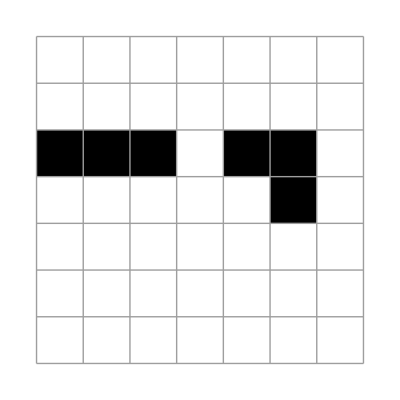

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/02_two_cell_comparison.m"];
looker2=plt[({{0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {xNW21, xN21, xNE21, xNW22, xN22, xNE22, 0}, {xW21, x21, xE21, xW22, x22, xE22, 0}, {xSW21, xS21, xSE21, xSW22, xS22, xSE22, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}})/.#]&;
(*X0=IntegerPart@ImageData@(looker2/@endGame)[[1]];*)

looker2/@endGame
```

```mathematica
Implies
```

```mathematica
⇒
```

```mathematica
cnf[x⇒False]
```

CNF | DNF
¬x | ¬x

```mathematica
life44
```

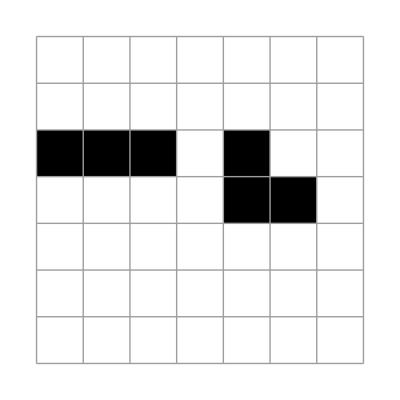
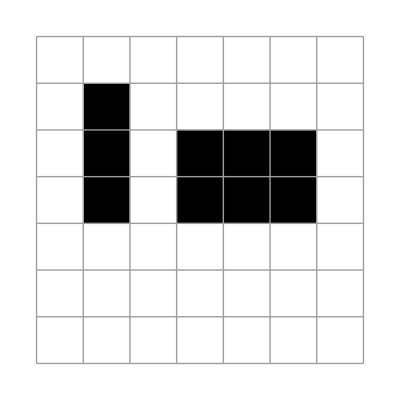
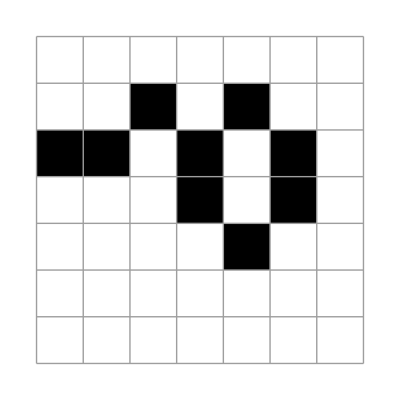
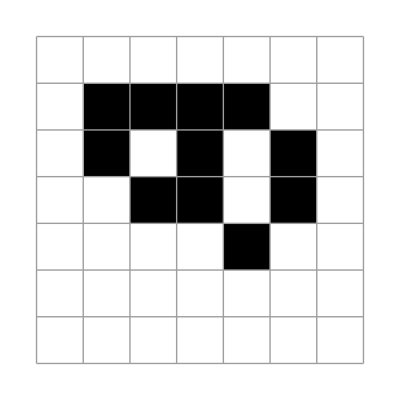

```mathematica
X0=({{0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {xNW21, xN21, xNE21, xNW22, xN22, xNE22, 0}, {xW21, x21, xE21, xW22, x22, xE22, 0}, {xSW21, xS21, xSE21, xSW22, xS22, xSE22, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}})/.endGame[[1]];
plt/@NestList[updateLife2[{7,7}][ #]&,
X0,3]
```